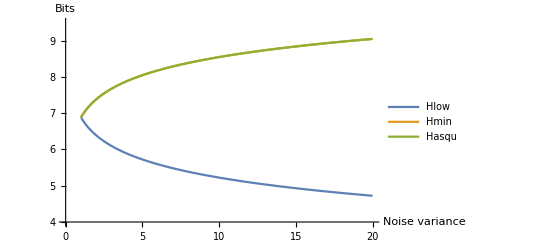

```mathematica
S0=1;
Hlow=-Log2[1/(2π)*dp*dq*S0]-2×Log2[√(dq/(√(π*z)))*EllipticTheta[3,0,ⅇ^(-dq^2/(2*z))]];
Hmin=-Log2[1/(√(π*z))dp];
Hasqu=-Log2[1/(2π)*dp*dq*S0]-2×Log2[√(dq/(√(π*(1/z))))*EllipticTheta[3,0,ⅇ^(-dq^2/(2*(1/z)))]];
m1=m2=0;
dp=dq=0.015;
Plot[{Hlow,Hmin,Hasqu},{z,1,20},PlotRange->{4,9.5},PlotLegends->"Expressions",AxesLabel->{Style[Noise variance],Style[Bits]}]
```